```mathematica
ClearAll["Global`*"];
```

```mathematica
ϵ=10^(-3);znak=4;

X0={-1,-2};α=1;
f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2;
(*f[{x_,y_}]:=(x+1)^2+y^2-15;*)
g[{x_,y_}]:=(3 x^2)/4+(5x)/4-2-y;
rk=Abs[(Grad[f[{x,y}],{x,y}].Grad[g[{x,y}],{x,y}])/Norm[Grad[g[{x,y}],{x,y}]]^2/.{x->X0[[1]],y->X0[[2]]}];
δk[{x_,y_}]:=-rk/g[{x,y}];
(*δk[{x_,y_}]:=-rk/g[{x,y}];*)
(*δk[{x_,y_}]:=-rk Log[-g[{x,y}]];*)
fk[{x_,y_}]:=f[{x,y}]+δk[{x,y}];
antiGradF[{x1_,x2_}]:=-Grad[fk[{x,y}],{x,y}]/.{x->x1,y->x2};
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]];
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}];


Hesse[{x1_,y1_}]:=D[fk[{x,y}],{{x,y},2}]/.{x->x1,y->y1};

i=0;κ=1;e={{1,0},{0,1}};
points={X0};
fValues={f[X0]};


While[True,(*метод внутренних штрафных*)

X=X0;
P={0,0};
norm=NormGradF[X0];
ω=antiGradF[X0];
H=Hesse[X0];
While[norm≥ϵ,(*метод Ньютона*)
While[PositiveDefiniteMatrixQ[H]==False,H+=10*e;];
P=LinearSolve[H,ω];
X+=N[κ*P,20];  
ω=antiGradF[X];i+=3;
H=Hesse[X];i+=9;

norm=NormGradF[X];                  
];
points=Append[points,X];
fValues=Append[fValues,f[X]];i++;
If[Abs[fk[points[[-1]]]-fk[points[[-2]]]]<ϵ,Break[];];
rk/=2;
];
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: точка минимума X = "<>ToString[SetAccuracy[X,znak]]<>" Функция f(x) в алгоритме была вычислена "<>ToString[i]<>" раз."
"Минимальное значение функции: f(X^*) = "
SetAccuracy[f[X],znak]
```

Результат получен за 9 итер.: точка минимума X = {0.987, 0.991} Функция f(x) в алгоритме была вычислена 729 раз.

Минимальное значение функции: f(X^*) =

0.0005

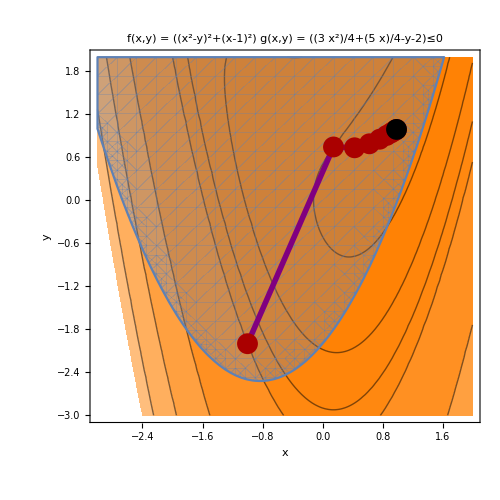

```mathematica
CP0={-3,-3}; CP1={2,2}; 
(*CP0={0,-1.1}; CP1={2.1,1.1};(*доп пример*)*)
 a:=Length[points]-1;b:=Length[points];
Show[ContourPlot[f[{x,y}],{x,CP0[[1]],CP1[[1]]},{y,CP0[[2]],CP1[[2]]},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),5]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;2]]~Join~{fValues[[a]],fValues[[b]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Column[{Text[Style["f(x,y) = ",Italic]f[{x,y}]],Text[Style["g(x,y) = ",Italic]g[{x,y}]≤0]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Purple,Thickness[0.008],Line[points],Darker[Red],PointSize[0.03],Point[points],Black,Point[points[[Length[points]]]]}],RegionPlot[g[{x,y}]≤0,{x,CP0[[1]],CP1[[1]]},{y,CP0[[2]],CP1[[2]]}]]
```